```mathematica
VegasNoIncrease1e3=Import["/home/johann/Documents/Projects/transportEquations/collision_cpp/vegas_no_increase_1e3.dat","Table"];
VegasNoIncrease1e4=Import["/home/johann/Documents/Projects/transportEquations/collision_cpp/vegas_no_increase_1e4.dat","Table"];
VegasWarmUp1e21e4=Import["/home/johann/Documents/Projects/transportEquations/collision_cpp/vegas_warmup_1e3_1e5_2.dat","Table"];
```

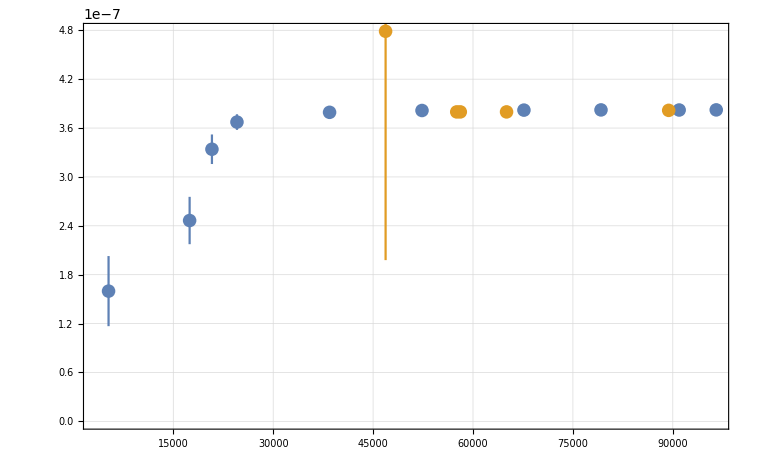

```mathematica
ErrorListPlot[{VegasNoIncrease1e4[[All,{3,1,2}]],VegasWarmUp1e21e4[[All,{3,1,2}]]},PlotTheme->"FrameGrid",PlotRange->All,FrameStyle->Thick]
```

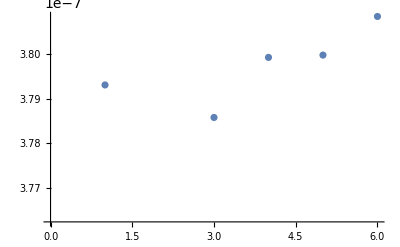

```mathematica
ListPlot[VegasWarmUp1e21e4[[All,1]]]
```

```mathematica
VegasWarmUp1e21e4
```

{{3.79825×10^-7,2.10272×10^-9,63474}}

```mathematica
2^8
```

256